## Solar Flares & CMEs Problem Set 2 Roy Smart

```mathematica
Clear["Global`*"]
```

## Problem 2

### From 1 to 1.01 solar radii we use the VAL model used by Hurford and Gary 2004

#### Import tabulated data from the VAL model

```mathematica
data=Transpose[Import[FileNameJoin[{NotebookDirectory[],"p2_modelB.csv"}]]];
```

#### Put units in terms of solar radii

```mathematica
h0 = data[[1]] / 695700;
```

#### The number density is the second column

```mathematica
N0 = data[[2]];
```

#### The plasma frequency is given as

```mathematica
νp[n_] := 8980 √n
```

#### Construct a plot of this region

```mathematica
ν0=Transpose[{νp[N0],h0}];
pltrng = {{10^4,5 10^10},{5 10^-4,10^3}};
p0=ListLogLogPlot[ν0,PlotRange->pltrng,Joined->True,ImageSize->Large];
```

### From 1.01 to 1.2 solar radii use model by Mann et al (1997)

#### The functional form given in the paper is

```mathematica
N2 = Ns Exp[A/Rs(1/R-1)] ;
A = (μ G Ms Mp)/(k T);
```

#### with the corresponding values

```mathematica
N2v = {Ns-> Min[N0], μ-> 0.6, G-> 6.674 10^-11,Ms-> 1.988 10^30, k-> 1.38 10^-23,T-> 2 10^6,Rs-> 6.957 10^8,Mp-> 1.672 10^-27};
```

#### Put equation in terms of frequency

```mathematica
R2 = Part[Solve[νp[N2]== ν,R]//Quiet,1,1,2]-1 /. N2v
```

-1+(1.33104×10^-7)/(1.33104×10^-7+1.92013×10^-8 Log[1.49587×10^-17 ν^2])

#### Find min and max frequency

```mathematica
Rmn = Max[h0]+1;
Rmx=2.3;
νmx = νp[N2] /. N2v /. R-> Rmn
νmn= νp[N2] /. N2v /. R-> Rmx
```

2.55252×10^8

3.64545×10^7

#### Construct plot of the region

```mathematica
p2=LogLogPlot[R2 /. N2v,{ν,νmn,νmx},PlotRange->pltrng,ImageSize->Large];
```

### From 1.2-215 solar radii we use the model given by Leblanc et al (1998)

#### The functional form is given as

```mathematica
N4 = α/R^2+β/R^4+γ/R^6;
```

#### The values given in the paper are

```mathematica
N4v={α-> 3.3 10^5,β-> 4.1 10^6,γ-> 8 10^7};
```

#### Put equation in terms of frequency

```mathematica
R4 = Part[Solve[νp[N4]== ν,R] //Quiet,2,1,2];
```

#### Find min and max frequency

```mathematica
Rmn = 1.33;
Rmx=300;
νmx = νp[N4] /. N4v /. R-> Rmn
νmn= νp[N4] /. N4v /. R-> Rmx
```

3.58645×10^7

17196.6

#### Construct plot of the region

```mathematica
p4=LogLogPlot[R4 /. N4v,{ν,νmn,νmx},PlotRange->pltrng,ImageSize->Large];
```

### Construct final plot

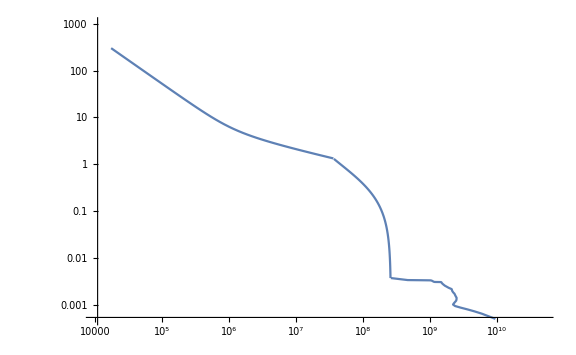

```mathematica
Show[p0,p2,p4,GridLines-> {{2.209723997441974*^6},{215}}]
```